```mathematica
Γ=1/2* (γl*nl+γu*nu);
```

```mathematica
n=2*γu* γl* f^2 (nl−nu)Γ/(Γ^2*γu γl  (3*nl* nu+nu+nl)+4*f^2*Γ(3*Γ+γu+γl));
```

```mathematica
a1=γl γu(Γ^2)(3nl nu+nu+nl)+4f^2 *Γ*(3Γ+γl+γu);
```

```mathematica
a2=(Γ^2+4f^2)* (4Γ+γl+γu)+2Γ*γl γu (3nl nu+nl+nu);

Fpop=(nu (nl+1)+nl (nu+1))/(nl−nu);
```

```mathematica
Ftr=-2*n*(a2/a1-Γ^(-1));
```

```mathematica
Q=Log[E,(nl(nu+1))/(nu(nl+1))]*Fpop+Log[E,(nl(nu+1))/(nu(nl+1))]*Ftr
```

(((1+nl) nu+nl (1+nu)) Log[(nl (1+nu))/((1+nl) nu)])/(nl-nu)-(2 f^2 (nl-nu) γl γu (nl γl+nu γu) (-2/(nl γl+nu γu)+((nl+nu+3 nl nu) γl γu (nl γl+nu γu)+(γl+γu+2 (nl γl+nu γu)) (4 f^2+1/4 (nl γl+nu γu)^2))/(1/4 (nl+nu+3 nl nu) γl γu (nl γl+nu γu)^2+2 f^2 (nl γl+nu γu) (γl+γu+3/2 (nl γl+nu γu)))) Log[(nl (1+nu))/((1+nl) nu)])/(1/4 (nl+nu+3 nl nu) γl γu (nl γl+nu γu)^2+2 f^2 (nl γl+nu γu) (γl+γu+3/2 (nl γl+nu γu)))

```mathematica
Q2[nu_]=Log[(nl(nu+1))/(nu(nl+1))]*((nu (nl+1)+nl (nu+1))/(nl−nu)-(2*2*γu* γl f^2 (nl−nu)(1/2* (γl*nl−γu*nu))/((1/2* (γl*nl−γu*nu))^2*γu γl  (3*nl* nu+nu+nl)+4*f^2*1/2* (γl*nl−γu*nu)(3*(1/2* (γl*nl−γu*nu))+γu+γl)))*((((1/2* (γl*nl−γu*nu))^2+4f^2)* (4*(1/2* (γl*nl−γu*nu))+γl+γu)+2*(1/2* (γl*nl−γu*nu))*γl γu (3nl nu+nl+nu))/(γl γu((1/2* (γl*nl−γu*nu))^2)(3nl nu+nu+nl)+4f^2 *(1/2* (γl*nl−γu*nu))*(3*(1/2* (γl*nl−γu*nu))+γl+γu))-(1/2* (γl*nl−γu*nu))^(-1)))
```

(((1+nl) nu+nl (1+nu))/(nl-nu)-(2 f^2 (nl-nu) γl γu (nl γl-nu γu) (-2/(nl γl-nu γu)+((nl+nu+3 nl nu) γl γu (nl γl-nu γu)+(γl+γu+2 (nl γl-nu γu)) (4 f^2+1/4 (nl γl-nu γu)^2))/(1/4 (nl+nu+3 nl nu) γl γu (nl γl-nu γu)^2+2 f^2 (nl γl-nu γu) (γl+γu+3/2 (nl γl-nu γu)))))/(1/4 (nl+nu+3 nl nu) γl γu (nl γl-nu γu)^2+2 f^2 (nl γl-nu γu) (γl+γu+3/2 (nl γl-nu γu)))) Log[(nl (1+nu))/((1+nl) nu)]

```mathematica
((1.027 nl+0.027 (1+nl)) Log[(38.03703703703704 nl)/(1+nl)])/(-0.027+nl)-(0.009 (-0.054+0.1 nl) (-0.027+nl) (-2/(-0.054+0.1 nl)+((2.1+2 (-0.054+0.1 nl)) (0.09+1/4 (-0.054+0.1 nl)^2)+0.2 (-0.054+0.1 nl) (0.027+1.081 nl))/(0.045 (2.1+3/2 (-0.054+0.1 nl)) (-0.054+0.1 nl)+0.05 (-0.054+0.1 nl)^2 (0.027+1.081 nl))) Log[(38.03703703703704 nl)/(1+nl)])/(0.045 (2.1+3/2 (-0.054+0.1 nl)) (-0.054+0.1 nl)+0.05 (-0.054+0.1 nl)^2 (0.027+1.081 nl))
```

```mathematica
Clear[f,γu,γl,nl,nu]
```

```mathematica
Clear[nu]
```

```mathematica
γl=0.1
γu=2
f=0.15
nl=5
```

0.1

2

0.15

5

```mathematica
""
```

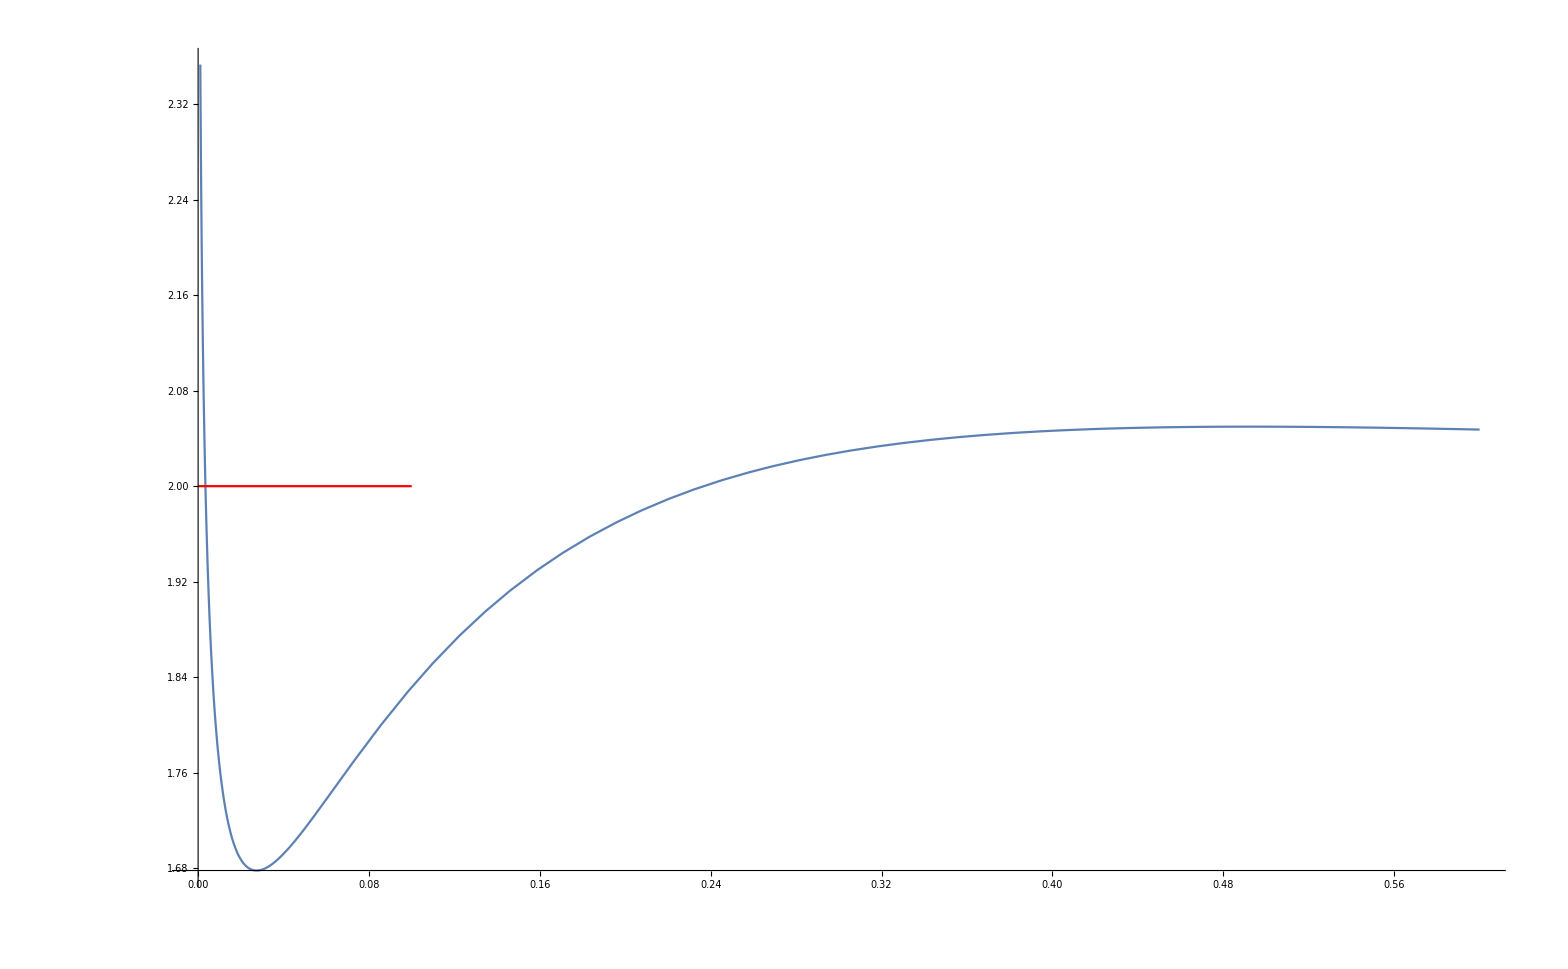

```mathematica
Show[Plot[Q,{nu,0.0,0.6}],Plot[2,{nu,0.0,0.1},PlotStyle->Red]]
```

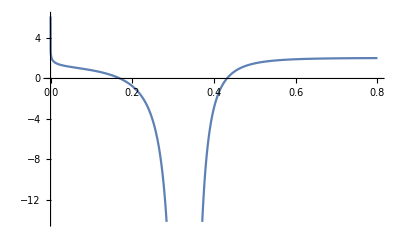

```mathematica
Plot[Q2[nu],{nu,0.0,0.8}]
```

```mathematica
FortranForm[Q]
```

(((1 + nc)*nh + nc*(1 + nh))*Log(((1 + nc)*nh)/(nc*(1 + nh))))/(-nc + nh) - 
     -  (2*epsilon**2*gammac*gammah*(-nc + nh)*(gammac*nc + gammah*nh)*
     -     (-2/(gammac*nc + gammah*nh) + (gammac*gammah*(gammac*nc + gammah*nh)*(nc + nh + 3*nc*nh) + 
     -          (gammac + gammah + 2*(gammac*nc + gammah*nh))*(4*epsilon**2 + (gammac*nc + gammah*nh)**2/4.))/
     -        ((gammac*gammah*(gammac*nc + gammah*nh)**2*(nc + nh + 3*nc*nh))/4. + 2*epsilon**2*(gammac*nc + gammah*nh)*(gammac + gammah + (3*(gammac*nc + gammah*nh))/2.)))*
     -     Log(((1 + nc)*nh)/(nc*(1 + nh))))/
     -   ((gammac*gammah*(gammac*nc + gammah*nh)**2*(nc + nh + 3*nc*nh))/4. + 2*epsilon**2*(gammac*nc + gammah*nh)*(gammac + gammah + (3*(gammac*nc + gammah*nh))/2.))